```mathematica
Сначала находим основное решение
```

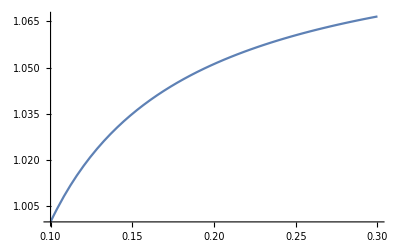

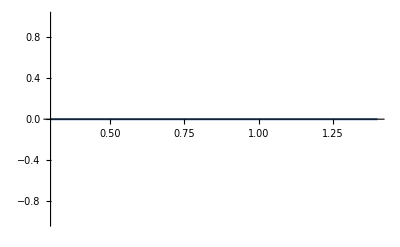

```mathematica
γ=2.0;
r1=0.3;
F=0.0;
s=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]*u[r]/ρ[r],u[0.1]==1,ρ[0.1]==1,p[0.1]==0.05},{ρ,u,p},{r,0.1,r1}];
Plot[u[x]/. s,{x, 0.1,r1}]
DD = 0;
ro1 =ρ[r1]/. s[[1]];
pp1 = p[r1]/. s[[1]];
uu1 = u[r1]/. s[[1]];
F=0.0;
g = 2.0;
ss = NSolve[ro1*(uu1-DD)==ro*(u-DD)&&ro1*uu1*(uu1 - DD) + pp1 == ro*u*(u - DD)+ p&& ro1*(uu1 - DD)*(pp1/(ro1*(g-1)) + uu1^2/2) + pp1 * uu1==ro*(u - DD)*(p/(ro*(g-1)) + (u^2)/2) + p * u ,{ro, u, p},Reals];
g1=u/. ss[[1]];
g2=ro/. ss[[1]];
g3=p/. ss[[1]];
r2=1.4;
sss=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]u[r]/ρ[r],u[r1]==g1,ρ[r1]==g2,p[r1]==g3},{ρ,u,p},{r,r1,r2}];
sss=NDSolve[{ρ'[r]==0, u'[r]==0,p'[r]==0,u[r1]==0,ρ[r1]==g2,p[r1]==g3},{ρ,u,p},{r,r1,r2}];
Plot[u[x]/. sss,{x, r1, r2}]
```

```mathematica
РЕШАЕМ ЛИНЕЙНУЮ ЗАДАЧУ
```

```mathematica
(*Простая функция линеаризации*)
LinearizeSingleEquation[eq_,baseVars_,pertVars_,eps_]:=Module[{},Coefficient[Normal[Series[eq,{eps,0,1}]],eps]];

(*Пример использования*)
u=u0+ε*u1[r,ϕ,t];
v=v0+ε*v1[r,ϕ,t];
ρ=ρ0+ε*ρ1[r,ϕ,t];
p=p0+ε*p1[r,ϕ,t];

(*Уравнение 1*)
eq1=D[ρ,t]+D[r*ρ*u,r]/r+D[ρ*v,ϕ]/r;
result1=LinearizeSingleEquation[eq1,{u0,v0,ρ0,p0},{u1,v1,ρ1,p1},ε]*r;

(*Уравнение 2*)
eq2=D[ρ*u,t]+D[r*(ρ*u*u+p),r]/r+D[ρ*u*v,ϕ]/r-ρ*v*v/r-p/r+F*u/ρ;
result2=LinearizeSingleEquation[eq2,{u0,v0,ρ0,p0},{u1,v1,ρ1,p1},ε]*r;

(*Уравнение 3*)
eq3=D[ρ*v,t]+D[r*ρ*u*v,r]/r+D[ρ*v*v+p,ϕ]/r+ρ*u*v/r+F*v/ρ;
result3=LinearizeSingleEquation[eq3,{u0,v0,ρ0,p0},{u1,v1,ρ1,p1},ε]*r;

(*Уравнение 4*)
eq4=D[p/(γ-1) + ρ*(u*u+v*v)/2,t]+D[r*u*(γ*p/(γ-1) + ρ*(u*u+v*v)/2),r]/r+D[v*(γ*p/(γ-1) + ρ*(u*u+v*v)/2),ϕ]/r+F*(u*u+v*v)/ρ;
result4=LinearizeSingleEquation[eq4,{u0,v0,ρ0,p0},{u1,v1,ρ1,p1},ε]*r;

Print["Результаты:"];
Print["Ур1: ",Simplify[result1]];
Print["Ур2: ",Simplify[result2]];
Print["Ур3: ",Simplify[result3]];
Print["Ур4: ",Simplify[result4]];
```

Результаты:

Ур1: ρ0 u1[r,ϕ,t]+u0 ρ1[r,ϕ,t]+r ρ1^(0,0,1)[r,ϕ,t]+ρ0 v1^(0,1,0)[r,ϕ,t]+v0 ρ1^(0,1,0)[r,ϕ,t]+r ρ0 u1^(1,0,0)[r,ϕ,t]+r u0 ρ1^(1,0,0)[r,ϕ,t]

Ур2: ((F r)/ρ0+2 u0 ρ0) u1[r,ϕ,t]-2 v0 ρ0 v1[r,ϕ,t]+u0^2 ρ1[r,ϕ,t]-v0^2 ρ1[r,ϕ,t]-(F r u0 ρ1[r,ϕ,t])/ρ0^2+r ρ0 u1^(0,0,1)[r,ϕ,t]+r u0 ρ1^(0,0,1)[r,ϕ,t]+v0 ρ0 u1^(0,1,0)[r,ϕ,t]+u0 ρ0 v1^(0,1,0)[r,ϕ,t]+u0 v0 ρ1^(0,1,0)[r,ϕ,t]+r p1^(1,0,0)[r,ϕ,t]+2 r u0 ρ0 u1^(1,0,0)[r,ϕ,t]+r u0^2 ρ1^(1,0,0)[r,ϕ,t]

Ур3: 2 v0 ρ0 u1[r,ϕ,t]+((F r)/ρ0+2 u0 ρ0) v1[r,ϕ,t]+2 u0 v0 ρ1[r,ϕ,t]-(F r v0 ρ1[r,ϕ,t])/ρ0^2+r ρ0 v1^(0,0,1)[r,ϕ,t]+r v0 ρ1^(0,0,1)[r,ϕ,t]+p1^(0,1,0)[r,ϕ,t]+2 v0 ρ0 v1^(0,1,0)[r,ϕ,t]+v0^2 ρ1^(0,1,0)[r,ϕ,t]+r v0 ρ0 u1^(1,0,0)[r,ϕ,t]+r u0 ρ0 v1^(1,0,0)[r,ϕ,t]+r u0 v0 ρ1^(1,0,0)[r,ϕ,t]

Ур4: 1/2 ((2 u0 γ p1[r,ϕ,t])/(-1+γ)+((2 p0 γ)/(-1+γ)+(4 F r u0)/ρ0+3 u0^2 ρ0+v0^2 ρ0) u1[r,ϕ,t]+(4 F r v0 v1[r,ϕ,t])/ρ0+2 u0 v0 ρ0 v1[r,ϕ,t]+u0^3 ρ1[r,ϕ,t]+u0 v0^2 ρ1[r,ϕ,t]-(2 F r u0^2 ρ1[r,ϕ,t])/ρ0^2-(2 F r v0^2 ρ1[r,ϕ,t])/ρ0^2+(2 r p1^(0,0,1)[r,ϕ,t])/(-1+γ)+2 r u0 ρ0 u1^(0,0,1)[r,ϕ,t]+2 r v0 ρ0 v1^(0,0,1)[r,ϕ,t]+r u0^2 ρ1^(0,0,1)[r,ϕ,t]+r v0^2 ρ1^(0,0,1)[r,ϕ,t]+(2 v0 γ p1^(0,1,0)[r,ϕ,t])/(-1+γ)+2 u0 v0 ρ0 u1^(0,1,0)[r,ϕ,t]+(2 p0 γ v1^(0,1,0)[r,ϕ,t])/(-1+γ)+u0^2 ρ0 v1^(0,1,0)[r,ϕ,t]+3 v0^2 ρ0 v1^(0,1,0)[r,ϕ,t]+u0^2 v0 ρ1^(0,1,0)[r,ϕ,t]+v0^3 ρ1^(0,1,0)[r,ϕ,t]+(2 r u0 γ p1^(1,0,0)[r,ϕ,t])/(-1+γ)+(2 p0 r γ u1^(1,0,0)[r,ϕ,t])/(-1+γ)+3 r u0^2 ρ0 u1^(1,0,0)[r,ϕ,t]+r v0^2 ρ0 u1^(1,0,0)[r,ϕ,t]+2 r u0 v0 ρ0 v1^(1,0,0)[r,ϕ,t]+r u0^3 ρ1^(1,0,0)[r,ϕ,t]+r u0 v0^2 ρ1^(1,0,0)[r,ϕ,t])

```mathematica
eqv1 =ρ0 u1[r,ϕ,t]+u0 ρ1[r,ϕ,t]+r Derivative[0,0,1][ρ1][r,ϕ,t]+ρ0 Derivative[0,1,0][v1][r,ϕ,t]+v0 Derivative[0,1,0][ρ1][r,ϕ,t]+r ρ0 Derivative[1,0,0][u1][r,ϕ,t]+r u0 Derivative[1,0,0][ρ1][r,ϕ,t];
eqv2 =((F r)/ρ0+2 u0 ρ0) u1[r,ϕ,t]-2 v0 ρ0 v1[r,ϕ,t]+u0^2 ρ1[r,ϕ,t]-v0^2 ρ1[r,ϕ,t]-(F r u0 ρ1[r,ϕ,t])/ρ0^2+r ρ0 Derivative[0,0,1][u1][r,ϕ,t]+r u0 Derivative[0,0,1][ρ1][r,ϕ,t]+v0 ρ0 Derivative[0,1,0][u1][r,ϕ,t]+u0 ρ0 Derivative[0,1,0][v1][r,ϕ,t]+u0 v0 Derivative[0,1,0][ρ1][r,ϕ,t]+r Derivative[1,0,0][p1][r,ϕ,t]+2 r u0 ρ0 Derivative[1,0,0][u1][r,ϕ,t]+r u0^2 Derivative[1,0,0][ρ1][r,ϕ,t];eqv3 =2 v0 ρ0 u1[r,ϕ,t]+((F r)/ρ0+2 u0 ρ0) v1[r,ϕ,t]+2 u0 v0 ρ1[r,ϕ,t]-(F r v0 ρ1[r,ϕ,t])/ρ0^2+r ρ0 Derivative[0,0,1][v1][r,ϕ,t]+r v0 Derivative[0,0,1][ρ1][r,ϕ,t]+Derivative[0,1,0][p1][r,ϕ,t]+2 v0 ρ0 Derivative[0,1,0][v1][r,ϕ,t]+v0^2 Derivative[0,1,0][ρ1][r,ϕ,t]+r v0 ρ0 Derivative[1,0,0][u1][r,ϕ,t]+r u0 ρ0 Derivative[1,0,0][v1][r,ϕ,t]+r u0 v0 Derivative[1,0,0][ρ1][r,ϕ,t];eqv4 =1/2 ((2 u0 γ p1[r,ϕ,t])/(-1+γ)+((2 p0 γ)/(-1+γ)+(4 F r u0)/ρ0+3 u0^2 ρ0+v0^2 ρ0) u1[r,ϕ,t]+(4 F r v0 v1[r,ϕ,t])/ρ0+2 u0 v0 ρ0 v1[r,ϕ,t]+u0^3 ρ1[r,ϕ,t]+u0 v0^2 ρ1[r,ϕ,t]-(2 F r u0^2 ρ1[r,ϕ,t])/ρ0^2-(2 F r v0^2 ρ1[r,ϕ,t])/ρ0^2+(2 r Derivative[0,0,1][p1][r,ϕ,t])/(-1+γ)+2 r u0 ρ0 Derivative[0,0,1][u1][r,ϕ,t]+2 r v0 ρ0 Derivative[0,0,1][v1][r,ϕ,t]+r u0^2 Derivative[0,0,1][ρ1][r,ϕ,t]+r v0^2 Derivative[0,0,1][ρ1][r,ϕ,t]+(2 v0 γ Derivative[0,1,0][p1][r,ϕ,t])/(-1+γ)+2 u0 v0 ρ0 Derivative[0,1,0][u1][r,ϕ,t]+(2 p0 γ Derivative[0,1,0][v1][r,ϕ,t])/(-1+γ)+u0^2 ρ0 Derivative[0,1,0][v1][r,ϕ,t]+3 v0^2 ρ0 Derivative[0,1,0][v1][r,ϕ,t]+u0^2 v0 Derivative[0,1,0][ρ1][r,ϕ,t]+v0^3 Derivative[0,1,0][ρ1][r,ϕ,t]+(2 r u0 γ Derivative[1,0,0][p1][r,ϕ,t])/(-1+γ)+(2 p0 r γ Derivative[1,0,0][u1][r,ϕ,t])/(-1+γ)+3 r u0^2 ρ0 Derivative[1,0,0][u1][r,ϕ,t]+r v0^2 ρ0 Derivative[1,0,0][u1][r,ϕ,t]+2 r u0 v0 ρ0 Derivative[1,0,0][v1][r,ϕ,t]+r u0^3 Derivative[1,0,0][ρ1][r,ϕ,t]+r u0 v0^2 Derivative[1,0,0][ρ1][r,ϕ,t]);
```

```mathematica
u1[r_,ϕ_,t_]:=U[r]*Exp[ⅈ*(m * ϕ-ω*t)];
v1[r_,ϕ_,t_]:=V[r]*Exp[ⅈ*(m * ϕ-ω*t)];
ρ1[r_,ϕ_,t_]:=R[r]*Exp[ⅈ*(m * ϕ-ω*t)];
p1[r_,ϕ_,t_]:=P[r]*Exp[ⅈ*(m * ϕ-ω*t)];
ξ[ϕ_,t_]:=Xi*Exp[ⅈ*(m * ϕ-ω*t)];
```

```mathematica
eqv1 /(ⅇ^(ⅈ (m ϕ-t ω)) )//FullSimplify
eqv2/(ⅇ^(ⅈ (m ϕ-t ω)) )//FullSimplify
eqv3/(ⅇ^(ⅈ (m ϕ-t ω)) )//FullSimplify
eqv4 /(ⅇ^(ⅈ (m ϕ-t ω)) )//FullSimplify
```

(u0+ⅈ (m v0-r ω)) R[r]+r u0 R'[r]+ρ0 (U[r]+ⅈ m V[r]+r U'[r])

(-(F r u0+ρ0^2 (-u0^2-ⅈ m u0 v0+v0^2+ⅈ r u0 ω)) R[r]+ρ0 ((F r+ρ0^2 (2 u0+ⅈ m v0-ⅈ r ω)) U[r]+ρ0 ((ⅈ m u0-2 v0) ρ0 V[r]+r (P'[r]+u0^2 R'[r]+2 u0 ρ0 U'[r]))))/ρ0^2

ⅈ m P[r]+v0 (2 u0+ⅈ m v0-(F r)/ρ0^2-ⅈ r ω) R[r]+2 v0 ρ0 U[r]+(F r V[r])/ρ0+2 u0 ρ0 V[r]+2 ⅈ m v0 ρ0 V[r]-ⅈ r ρ0 ω V[r]+r u0 v0 R'[r]+r v0 ρ0 U'[r]+r u0 ρ0 V'[r]

1/(2 (-1+γ) ρ0^2)(2 ρ0^2 (u0 γ+ⅈ (m v0 γ-r ω)) P[r]+(u0^2+v0^2) (-1+γ) (-2 F r+ρ0^2 (u0+ⅈ (m v0-r ω))) R[r]+ρ0 ((4 F r u0 (-1+γ)+ρ0 (2 p0 γ+(-1+γ) ρ0 (3 u0^2+v0^2+2 ⅈ u0 (m v0-r ω)))) U[r]+(4 F r v0 (-1+γ)+ⅈ ρ0 (2 m p0 γ+m (u0^2+3 v0^2) (-1+γ) ρ0-2 ⅈ v0 (-1+γ) ρ0 (u0-ⅈ r ω))) V[r]+r ρ0 (2 u0 γ P'[r]+u0 (u0^2+v0^2) (-1+γ) R'[r]+(2 p0 γ+(3 u0^2+v0^2) (-1+γ) ρ0) U'[r]+2 u0 v0 (-1+γ) ρ0 V'[r])))

```mathematica
yr1[r_]:=(u0+ⅈ (m v0-r ω)) R[r]+r u0 R'[r]+ρ0 (U[r]+ⅈ m V[r]+r U'[r]);
yr2[r_]:=(-(F r u0+ρ0^2 (-u0^2-ⅈ m u0 v0+v0^2+ⅈ r u0 ω)) R[r]+ρ0 ((F r+ρ0^2 (2 u0+ⅈ m v0-ⅈ r ω)) U[r]+ρ0 ((ⅈ m u0-2 v0) ρ0 V[r]+r (P'[r]+u0^2 R'[r]+2 u0 ρ0 U'[r]))))/ρ0^2;
yr3[r_]:=ⅈ m P[r]+v0 (2 u0+ⅈ m v0-(F r)/ρ0^2-ⅈ r ω) R[r]+2 v0 ρ0 U[r]+(F r V[r])/ρ0+2 u0 ρ0 V[r]+2 ⅈ m v0 ρ0 V[r]-ⅈ r ρ0 ω V[r]+r u0 v0 R'[r]+r v0 ρ0 U'[r]+r u0 ρ0 V'[r];
yr4[r_]:=1/(2 (-1+γ) ρ0^2)(2 ρ0^2 (u0 γ+ⅈ (m v0 γ-r ω)) P[r]+(u0^2+v0^2) (-1+γ) (-2 F r+ρ0^2 (u0+ⅈ (m v0-r ω))) R[r]+ρ0 ((4 F r u0 (-1+γ)+ρ0 (2 p0 γ+(-1+γ) ρ0 (3 u0^2+v0^2+2 ⅈ u0 (m v0-r ω)))) U[r]+(4 F r v0 (-1+γ)+ⅈ ρ0 (2 m p0 γ+m (u0^2+3 v0^2) (-1+γ) ρ0-2 ⅈ v0 (-1+γ) ρ0 (u0-ⅈ r ω))) V[r]+r ρ0 (2 u0 γ P'[r]+u0 (u0^2+v0^2) (-1+γ) R'[r]+(2 p0 γ+(3 u0^2+v0^2) (-1+γ) ρ0) U'[r]+2 u0 v0 (-1+γ) ρ0 V'[r])));
```

```mathematica
F=0;
R1 = 0.3;
R2 = 1.4;
Num=10; (* число точек коллокации внутри области*)
xk[k_]:=R1 + (1+Cos[π*(k-0.5)/Num])/2 * (R2 - R1)//N;
collocationPoints=Table[xk[k],{k,Num}];
equations={yr1,yr2,yr3,yr4};
basis[n_,r_]:=ChebyshevT[n,(2*(r-R1)/(R2-R1))-1];
R[r_]:=Sum[kr[n]*basis[n,r],{n,0,Num }];
U[r_]:=Sum[ku[n]*basis[n,r],{n,0,Num }];
V[r_]:=Sum[kv[n]*basis[n,r],{n,0,Num }];
P[r_]:=Sum[kp[n]*basis[n,r],{n,0,Num }];
variables=Join[Table[kr[i],{i,0,Num }],Table[ku[i],{i,0,Num }],Table[kv[i],{i,0,Num }],Table[kp[i],{i,0,Num }], {Xi}]
nVars=Length[variables];
u0[r_]=1.0;
v0[r_]=0.0;
ρ0[r_]=ρ[r]/. sss;
p0[r_]=p[r]/. sss;
```

{kr[0],kr[1],kr[2],kr[3],kr[4],kr[5],kr[6],kr[7],kr[8],kr[9],kr[10],ku[0],ku[1],ku[2],ku[3],ku[4],ku[5],ku[6],ku[7],ku[8],ku[9],ku[10],kv[0],kv[1],kv[2],kv[3],kv[4],kv[5],kv[6],kv[7],kv[8],kv[9],kv[10],kp[0],kp[1],kp[2],kp[3],kp[4],kp[5],kp[6],kp[7],kp[8],kp[9],kp[10],Xi}

```mathematica
collocationPoints
```

{1.39323,1.34005,1.23891,1.09969,0.936039,0.763961,0.600305,0.461091,0.359946,0.306771}

```mathematica
(*Инициализация матриц A и B*)
A={};
B={};
(*Цикл по всем уравнениям и точкам коллокации*)
Do[Do[(*Вычисляем уравнение в текущей точке*)
currentEquation=equations[[eqIndex]][collocationPoints[[pointIndex]]];
(*Разделяем на части с ω и без ω*)
equationWithoutOmega=currentEquation/. ω->0;
equationOmegaPart=currentEquation-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];,
{pointIndex,Length[collocationPoints]}],
{eqIndex,Length[equations]}];
```

```mathematica
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
Print["Количество уравнений: ",Length[equations]*Length[collocationPoints]]
Print["Количество переменных: ",nVars]
```

Размер матрицы A: {40,45,1}

Размер матрицы B: {40,45,1}

Количество уравнений: 40

Количество переменных: 45

```mathematica
Добавим уравнения на граничные условия
```

```mathematica
(*Жёсткое Правое граничное условие*)
```

```mathematica
boundaryRowA=Table[Coefficient[P[R2],variables[[i]]],{i,nVars}];
boundaryRowB=ConstantArray[0,nVars];
AppendTo[A,boundaryRowA];
AppendTo[B,boundaryRowB];
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
```

Размер матрицы A: {41,45}

Размер матрицы B: {41,45}

```mathematica
(*Мягкое Правое граничное условие*)
boundaryRowA=Table[Coefficient[D[P[r],r]/. r->R2,variables[[i]]],{i,nVars}];
boundaryRowB=ConstantArray[0,nVars];
AppendTo[A,boundaryRowA];
AppendTo[B,boundaryRowB];
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
```

Размер матрицы A: {41,45}

Размер матрицы B: {41,45}

```mathematica
(*1 Неотражающее Правое граничное условие*)
boundaryRowA=Table[Coefficient[P[r]-ρ0[r]*Sqrt[γ*p0[r]/ρ0[r]]*U[r]/. r->R2,variables[[i]]],{i,nVars}];
boundaryRowB=ConstantArray[0,nVars];
AppendTo[A,boundaryRowA];
AppendTo[B,boundaryRowB];
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
```

Размер матрицы A: {41,45,1}

Размер матрицы B: {41,45}

```mathematica
(*2 Неотражающее Правое граничное условие - второй вариант*)
beq1=(p1[R2,ϕ,t]-ρ0[R2]*Sqrt[γ*p0[R2]/ρ0[R2]]*u1[R2,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
equationWithoutOmega=beq1/. ω->0;
equationOmegaPart=beq1-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];
```

```mathematica
(*Левое граничное условие*)
```

```mathematica
beq1=(ρ0[R1]*u1[R1,ϕ,t]+u0[R1]*ρ1[R1,ϕ,t]-ⅈ*ω*ξ[ϕ,t]*(ro1-ρ0[R1]))/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq2=(v1[R1,ϕ,t]-(uu1-u0[R1])*ⅈ*ξ[ϕ,t]/R1)/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq3=(2*ρ0[R1]*u0[R1]*u1[R1,ϕ,t]+u0[R1]*u0[R1]*ρ1[R1,ϕ,t]+p1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq4=(p1[R1,ϕ,t]-γ*p0[R1]/ρ0[R1] * ρ1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
```

```mathematica
(*Нулевое Левое граничное условие*)
beq1=(u1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq2=(ξ[ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq3=(ρ1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq4=(p1[R1,ϕ,t]-)/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
beq5=(γ/(γ-1) * (p1[R1,ϕ,t]/ρ0[R1] - p0[R1]*ρ1[R1,ϕ,t]/(ρ0[R1]*ρ0[R1])) + u0[R1]*u1[R1,ϕ,t]+v0[R1]*v1[R1,ϕ,t])/(ⅇ^(ⅈ (m ϕ-t ω)))//FullSimplify;
```

```mathematica
equationWithoutOmega=beq1/. ω->0;
equationOmegaPart=beq1-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];

equationWithoutOmega=beq2/. ω->0;
equationOmegaPart=beq2-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];

equationWithoutOmega=beq3/. ω->0;
equationOmegaPart=beq3-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];

equationWithoutOmega=beq4/. ω->0;
equationOmegaPart=beq4-equationWithoutOmega;
(*Вычисляем строки для матриц A и B*)
rowA=Table[Coefficient[equationWithoutOmega,variables[[i]]],{i,nVars}];
rowB=Table[Coefficient[equationOmegaPart,ω*variables[[i]]],{i,nVars}];
(*Добавляем строки в матрицы*)
AppendTo[A,rowA];
AppendTo[B,rowB];
```

```mathematica
Print["Размер матрицы A: ",Dimensions[A]]
Print["Размер матрицы B: ",Dimensions[B]]
```

Размер матрицы A: {45,45}

Размер матрицы B: {45,45}

```mathematica
Aflat=Table[If[Head[A[[i,j]]]===List,A[[i,j,1]],A[[i,j]]],{i,Dimensions[A][[1]]},{j,Dimensions[A][[2]]}];
Bflat=Table[If[Head[B[[i,j]]]===List,B[[i,j,1]],B[[i,j]]],{i,Dimensions[B][[1]]},{j,Dimensions[B][[2]]}];
boundaryIndices=Flatten[Position[Map[Total[Abs[#]]&,Bflat],0]];
interiorIndices=Complement[Range[Dimensions[B][[1]]],boundaryIndices];
Cmatrix=Aflat[[boundaryIndices]];
kernelBasis=NullSpace[Cmatrix];
Print["Размерность подпространства: ",Length[kernelBasis]];
(*4. Строим матрицу проекции V*)
V=Transpose[kernelBasis];  (*Столбцы V-базисные векторы*)
(*5. Проецируем матрицы на подпространство*)
Aproj=Transpose[V].Aflat.V;
Bproj=Transpose[V].Bflat.V;
Print["Размер A_proj: ",Dimensions[Aproj]];
Print["Размер B_proj: ",Dimensions[Bproj]];
```

Размерность подпространства: 30

Размер A_proj: {30,30}

Размер B_proj: {30,30}

```mathematica
mValue=1;  (*например*)
An=N[Aproj/. m->mValue];
Bn=N[Bproj/. m->mValue];
eigenvalues=Eigenvalues[{An,Bn}]
```

{-8.08666×10^-8+1.01191×10^-6 ⅈ,8.08665×10^-8-1.01191×10^-6 ⅈ,-4.30778×10^-15+2.53645×10^-14 ⅈ,1.15159×10^-14+7.042×10^-15 ⅈ,2.94966×10^-15+7.78244×10^-15 ⅈ,-6.79537×10^-15+2.43773×10^-15 ⅈ,6.75325×10^-16-2.65327×10^-15 ⅈ,-1.10676×10^-15-2.03415×10^-15 ⅈ,1.29238×10^-15-1.6566×10^-16 ⅈ,-9.88234×10^-16+4.41284×10^-16 ⅈ,-4.66304×10^-16+5.12341×10^-16 ⅈ,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}